```mathematica
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/autoindent.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"];
```

OpenWrite::aofil: /Users/khenisey/Documents/Github/covidmodel/model/autoindent.wl already open as /Users/khenisey/Documents/Github/covidmodel/model/autoindent.wl.

OpenWrite::noopen: Cannot open /Users/khenisey/Documents/Github/covidmodel/model/autoindent.wl.

Fitting model for CA

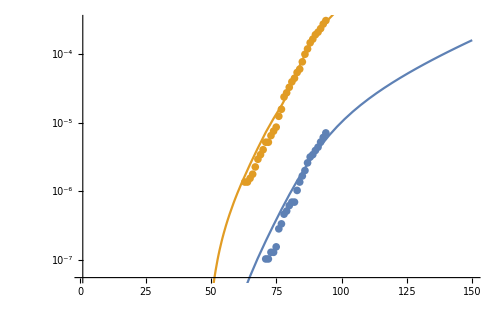
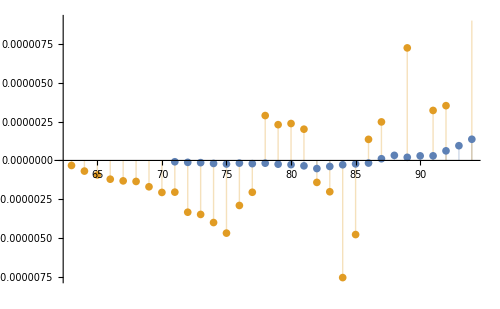
>> Fit for CA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.03465 | 0.0513633 | 59.0822 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[59.0822,53.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 46.6547 | 0.591169 | 78.9194 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[78.9194,53.,HypothesisTesting`TwoSided→True]
ⅇ^reportingLag | 6.07206 | 0.493683 | 12.2995 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[12.2995,53.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 3 | 1.55293×10^-12 | 5.17645×10^-13
Error | 53 | 3.3714×10^-14 | 6.36114×10^-16
Uncorrected Total | 56 | 1.58665×10^-12 | 
Corrected Total | 55 | 1.54274×10^-12 |

>> Current scenario Generating simulations for CA in the

>> Generating simulations for CA in the  Italy scenario

>> Generating simulations for CA in the  Wuhan scenario

>> Generating simulations for CA in the  Normal scenario

<|CA→<|scenarios→<|scenario1→<|distancingLevel→23/50,id→scenario1,4,events→{1},summary→<|totalProjectedDeaths→196285.,totalProjectedPCRConfirmed→3.61179×10^6,5,dateHospitalsOverCapacity→Tue 21 Jul 2020 21:38:12|>|>,2,1|>,13,1|>|>
 |  |  |  |

```mathematica
asd=GenerateModelExport[15,{"CA"}]
```